# QFT Series Expansion

## Operators

```mathematica
Sp = {{0,0},{1, 0}};
Sm= {{0,1}, {0,0}};
Sz = {{1/2, 0}, {0 ,-1/2}};
```

```mathematica
Ops ={Sp, Sm, Sz, IdentityMatrix[2]};
```

## Non-interacting Fields

### External Magnetic Field

```mathematica
hm=0;
hp=0;
hz=1;
```

```mathematica
Clear[hz]
```

```mathematica
Clear[hm, hp, hz]
```

```mathematica
Hb = {{hz, hm}, {hp, -hz}};
```

```mathematica
MatrixExp[β Hb]//ExpToTrig
```

{{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}}

```mathematica
HbExp[β_]:={{Cosh[√(hm hp+hz^2) β]+(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),(hm Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))},{(hp Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2)),Cosh[√(hm hp+hz^2) β]-(hz Sinh[√(hm hp+hz^2) β])/(√(hm hp+hz^2))}};
```

### Correlations

```mathematica
Corr[OpsList_, β_]:=Module[{op, n, i}, 
op = IdentityMatrix[2];
n= Length[OpsList];
For[i =1, i <=  n, i++, op = op.HbExp[OpsList[[i]][[2]]]. Ops[[OpsList[[i]][[1]]]].HbExp[-OpsList[[i]][[2]]]];
op = op. HbExp[β];
Return[Tr[op]];
]
```

#### Examples

```mathematica
OpsList = {{3, 1/10}, {3, 1/5}};
```

```mathematica
Corr[OpsList, β]//Simplify
```

Cosh[β]/2

```mathematica
Corr[OpsList, 1]//Simplify
```

(1+ⅇ^2)/(4 ⅇ)

```mathematica
OpsList = {};
Corr[OpsList, β]//Simplify
```

2 Cosh[√(hz^2) β]

## Interacting Fields

### Lattice

```mathematica
L=2;
Λ = Table[{i, 0, 0}, {i, 0, L-1}];
λ = Length[Λ];
```

### Metric Distance

```mathematica
a=1;
b=1;
c=1;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
```

```mathematica
d[v_, w_]:=Norm[LS.(v-w)];
```

```mathematica
d[Λ[[1]], Λ[[2]]]
```

6

### Interaction Tensors

#### XXZ

```mathematica
J=1;
V[v1_,v2_, s1_, s2_]:= If[Norm[v1-v2]==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) ||(s1==3&&s2==3), J, 0], 0];
```

```mathematica
V[{0,0,0}, {1, 0, 0}, 3, 3]
```

1

#### XX

```mathematica
J=1;
V[v1_,v2_, s1_, s2_]:= If[Norm[v1-v2]==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , J, 0], 0];
```

```mathematica
V[{1,0, 0}, {2, 0, 0}, 1, 2]V[{1, 0, 0}, {1, 0, 0}, 1 ,2]
```

0

### Interaction Paths

```mathematica
Interactions[λ_,len_]:=Module[{int ,Paths, SpinLabels, i, j},
Paths = Tuples[Range[λ],2 len];
SpinLabels =Tuples[{1,2,3}, 2 len];
int={};
For[i=1, i <= Length[Paths], i++,
For[j=1, j <= Length[SpinLabels], j++,If[Product[V[Λ[[Paths[[i]][[2k-1]]]],Λ[[Paths[[i]][[2k]]]] , SpinLabels[[j]][[2k-1]], SpinLabels[[j]][[2k]]], {k, 1, len}]!= 0, AppendTo[int, {Paths[[i]], SpinLabels[[j]]}]] ]
];
Return[int];
]
```

```mathematica
Inter1 =Interactions[λ, 1]
```

{{{1,2},{1,2}},{{1,2},{2,1}},{{2,1},{1,2}},{{2,1},{2,1}}}

### Interaction Contribution

```mathematica
InteractionContribution[λ_, path_, β_]:=Module[{OpsLists, i, τ,InterTerm, InterCoupling,k, n},
n=Length[path[[1]]]/2;
OpsLists = Table[{}, {i, 1, λ}];
If[n==0, Return[Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}]]];
For[i=1, i <= 2n, i++, AppendTo[OpsLists[[path[[1]][[i]]]], {path[[2]][[i]], τ[Floor[(i+1)/2]]}]];
InterTerm =Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}];
InterCoupling = Product[V[path[[1]][[2 i-1]], path[[1]][[2 i]], path[[2]][[2 i-1]], path[[2]][[2 i]]], {i,1, Length[path[[1]]]/2}];
Return[(1/(n!)) Integrate[InterCoupling* InterTerm, Sequence@@Table[{τ[k], 0, β}, {k, 1, n}]]];
]
NInteractionContribution[λ_, path_, β_]:=Module[{OpsLists, i, τ,InterTerm, InterCoupling,k, n},
n=Length[path[[1]]]/2;
OpsLists = Table[{}, {i, 1, λ}];
If[n==0, Return[Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}]]];
For[i=1, i <= 2n, i++, AppendTo[OpsLists[[path[[1]][[i]]]], {path[[2]][[i]], τ[Floor[(i+1)/2]]}]];
InterTerm =Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}];
InterCoupling = Product[V[path[[1]][[2 i-1]], path[[1]][[2 i]], path[[2]][[2 i-1]], path[[2]][[2 i]]], {i,1, Length[path[[1]]]/2}];
Return[(1/(n!)) NIntegrate[InterCoupling* InterTerm, Table[τ[k], {k, 1, n}]∈Cuboid[Table[0, {k, 1,n}], Table[β, {k, 1, n}]]]];
]
```

#### Examples

```mathematica
path = Inter1[[1]];
InteractionContribution[λ, path, β]
```

0

```mathematica
path = Interactions[λ, 0][[1]];
InteractionContribution[λ, path, β]
```

4 Cosh[√(hz^2) β]^2

#### Example: XX

```mathematica
path =Interactions[λ, 2][[2]]
InteractionContribution[λ, path, β]
```

{{1,2,1,2},{1,2,2,1}}

β^2/2

```mathematica
path =Interactions[λ, 2][[5]]
InteractionContribution[λ, path, β]
```

{{1,2,2,1},{1,2,1,2}}

β^2/2

#### Example:XX

```mathematica
path = Interactions[λ, 1][[3]]
InteractionContribution[λ, path, β]
```

{{1,2},{3,3}}

-β/2+1/4 ⅇ^(-2 √(hz^2) β) β+1/4 ⅇ^(2 √(hz^2) β) β

```mathematica
path = Interactions[λ, 1][[6]]
InteractionContribution[λ, path, β]
```

{{2,1},{3,3}}

-β/2+1/4 ⅇ^(-2 √(hz^2) β) β+1/4 ⅇ^(2 √(hz^2) β) β

## Partition Function

```mathematica
Z[deg_, β_]:=Module[{paths, i, len},
paths = Flatten[Table[Interactions[λ, len], {len, 0, deg}],1];
Return[Sum[InteractionContribution[λ, paths[[i]], β], {i, 1, Length[paths]}]]
 ]
NZ[deg_, β_]:=Module[{paths, i, len},
paths = Flatten[Table[Interactions[λ, len], {len, 0, deg}],1];
Return[Sum[NInteractionContribution[λ, paths[[i]], β], {i, 1, Length[paths]}]]
 ]
```

#### Example: XX

```mathematica
Hxx= ({{2hz, 0, 0, 0}, {0, 0, 2, 0}, {0, 2, 0, 0}, {0, 0, 0, -2hz}});
Tr[MatrixExp[β Hxx]]
Series[Tr[MatrixExp[β Hxx]], {β, 0, 4}]
```

ⅇ^(-2 β)+ⅇ^(2 β)+ⅇ^(-2 hz β)+ⅇ^(2 hz β)

4+(4+4 hz^2) β^2+4/3 (1+hz^4) β^4+O[β]^5

```mathematica
Z[1, β]
```

-β+1/2 ⅇ^(-2 β) β+1/2 ⅇ^(2 β) β+4 Cosh[β]^2

```mathematica
NZ[1, 1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

12.2866

```mathematica
Z[2, β]
```

-β+1/2 ⅇ^(-2 β) β+1/2 ⅇ^(2 β) β+4 β^2+4 Cosh[β]^2+1/2 β^2 Cosh[β]^2

```mathematica
NZ[2, 1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

17.4771

```mathematica
Z[3, β]
```

-β+1/2 ⅇ^(-2 β) β+1/2 ⅇ^(2 β) β+4 β^2-2 β^3+4 Cosh[β]^2+1/2 β^2 Cosh[β]^2+1/12 β^3 Sinh[β]^2

```mathematica
NZ[3, 1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

15.5922

```mathematica
z2 = Z[4, β]
```

4 β^2+(4 β^4)/3+4 Cosh[√(hz^2) β]^2

```mathematica
Series[z2, {β, 0, 4}]
```

4+(4+4 hz^2) β^2+4/3 (1+hz^4) β^4+O[β]^5

#### Example: XXZ

```mathematica
Hxxx= ({{2 hz-1/2, 0, 0, 0}, {0, 1/2, 2, 0}, {0, 2, 1/2, 0}, {0, 0, 0, -2 hz-1/2}});
Tr[MatrixExp[β Hxxx]]
Series[Tr[MatrixExp[β Hxxx]], {β, 0, 2}]
```

ⅇ^(-3 β/2)+ⅇ^(5 β/2)+ⅇ^(1/2 (-1+4 hz) β)+ⅇ^(-1/2 (1+4 hz) β)

4+1/2 (9+8 hz^2) β^2+O[β]^3

```mathematica
z2 = Z[2, β]
```

-β+1/2 ⅇ^(-2 √(hz^2) β) β+1/2 ⅇ^(2 √(hz^2) β) β+4 β^2+1/2 β^2 Cosh[hz β]^2+4 Cosh[√(hz^2) β]^2

```mathematica
Series[z2, {β, 0, 2}]
```

4+(9/2+4 hz^2) β^2+O[β]^3

## One-point Correlation Function

### Contributions

```mathematica
OnePointContribution[λ_, path_, β_,vertexIndex_, spinIndex_, t_]:=Module[{OpsLists, i, τ,InterTerm, InterCoupling,k, n},
n=Length[path[[1]]]/2;
OpsLists = Table[{}, {i, 1, λ}];
For[i=1, i <= 2n, i++, AppendTo[OpsLists[[path[[1]][[i]]]], {path[[2]][[i]], τ[Floor[(i+1)/2]]}]];
AppendTo[OpsLists[[vertexIndex]], {spinIndex, t}];
InterTerm =Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}];
If[n==0, Return[InterTerm]];
InterCoupling = Product[V[path[[1]][[2 i-1]], path[[1]][[2 i]], path[[2]][[2 i-1]], path[[2]][[2 i]]], {i,1, Length[path[[1]]]/2}];
Return[(1/(n!)) Integrate[InterCoupling* InterTerm, Sequence@@Table[{τ[k], 0, β}, {k, 1, n}]]];
]
NOnePointContribution[λ_, path_, β_,vertexIndex_, spinIndex_, t_]:=Module[{OpsLists, i, τ,InterTerm, InterCoupling,k, n},
n=Length[path[[1]]]/2;
OpsLists = Table[{}, {i, 1, λ}];
For[i=1, i <= 2n, i++, AppendTo[OpsLists[[path[[1]][[i]]]], {path[[2]][[i]], τ[Floor[(i+1)/2]]}]];
AppendTo[OpsLists[[vertexIndex]], {spinIndex, t}];
InterTerm =Product[Corr[OpsLists[[i]], β], {i, 1, Length[OpsLists]}];
If[n==0, Return[InterTerm]];
InterCoupling = Product[V[path[[1]][[2 i-1]], path[[1]][[2 i]], path[[2]][[2 i-1]], path[[2]][[2 i]]], {i,1, Length[path[[1]]]/2}];
Return[(1/(n!)) NIntegrate[InterCoupling* InterTerm, Table[τ[k], {k, 1, n}]∈Cuboid[Table[0, {k, 1,n}], Table[β, {k, 1, n}]]]];
]
```

#### Example: XX

```mathematica
path =Interactions[λ, 0][[1]]
```

{{},{}}

```mathematica
path =Interactions[λ, 0][[1]]
InteractionContribution[λ, path, β]
OnePointContribution[λ, path, β, 1, 3, t]//Simplify
```

{{},{}}

4 Cosh[√(hz^2) β]^2

(hz Sinh[2 √(hz^2) β])/(√(hz^2))

```mathematica
path =Interactions[λ, 2][[2]]
InteractionContribution[λ, path, β]
OnePointContribution[λ, path, β, 1, 3, t]
```

{{1,2,1,2},{1,2,2,1}}

β^2/2

-β^2/4

### Expansion

```mathematica
OnePoint[deg_, β_, vertexIndex_, spinIndex_, t_]:=Module[{paths, i, len},
paths = Flatten[Table[Interactions[λ, len], {len, 0, deg}],1];
Return[Sum[OnePointContribution[λ, paths[[i]], β, vertexIndex, spinIndex, t], {i, 1, Length[paths]}]]
 ]
NOnePoint[deg_, β_, vertexIndex_, spinIndex_, t_]:=Module[{paths, i, len},
paths = Flatten[Table[Interactions[λ, len], {len, 0, deg}],1];
Return[Sum[NOnePointContribution[λ, paths[[i]], β, vertexIndex, spinIndex, t], {i, 1, Length[paths]}]]
 ]
```

#### Example: XX

```mathematica
Hxx= ({{2hz, 0, 0, 0}, {0, 0, 2, 0}, {0, 2, 0, 0}, {0, 0, 0, -2hz}});
Sz1=({{1/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -1/2}});
Tr[Sz1.MatrixExp[β Hxx]]
Series[Tr[Sz1.MatrixExp[β Hxx]], {β, 0, 5}]
Series[Tr[MatrixExp[(β/2) Hxx].Sz1.MatrixExp[(β/2) Hxx]], {β, 0, 4}]
Series[Tr[Sz1.MatrixExp[β Hxx]]/Tr[MatrixExp[β Hxx]], {β, 0, 4}]
```

-1/2 ⅇ^(-2 hz β)+1/2 ⅇ^(2 hz β)+1/2 (-1/2 ⅇ^(-2 β)-ⅇ^(2 β)/2)+1/2 (ⅇ^(-2 β)/2+ⅇ^(2 β)/2)

2 hz β+(4 hz^3 β^3)/3+(4 hz^5 β^5)/15+O[β]^6

2 hz β+(4 hz^3 β^3)/3+O[β]^5

(hz β)/2+1/6 (-3 hz-hz^3) β^3+O[β]^5

```mathematica
Oxx = OnePoint[2, β, 1, 3, t]//Simplify
```

(hz Sinh[2 √(hz^2) β])/(√(hz^2))

```mathematica
Series[Oxx, {β, 0, 5}]
```

2 hz β+(4 hz^3 β^3)/3+(4 hz^5 β^5)/15+O[β]^6

#### Example: XXZ

```mathematica
Hxxz= ({{2 hz+1/2, 0, 0, 0}, {0, -1/2, 2, 0}, {0, 2, -1/2, 0}, {0, 0, 0, -2 hz+1/2}});
Sz1=({{1/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -1/2}});
Tr[Sz1.MatrixExp[β Hxxz]]
Series[Tr[Sz1.MatrixExp[β Hxxz]], {β, 0, 4}]
Series[Tr[MatrixExp[(β/2) Hxxz].Sz1.MatrixExp[(β/2) Hxxz]], {β, 0, 4}]
Series[Tr[Sz1.MatrixExp[β Hxxz]]/Tr[MatrixExp[β Hxxz]], {β, 0, 4}]
```

-1/2 ⅇ^(-1/2 (-1+4 hz) β)+1/2 ⅇ^(1/2 (1+4 hz) β)+1/2 (-1/2 ⅇ^(-5 β/2)-1/2 ⅇ^(3 β/2))+1/2 (1/2 ⅇ^(-5 β/2)+1/2 ⅇ^(3 β/2))

2 hz β+hz β^2+1/12 (3 hz+16 hz^3) β^3+1/24 (hz+16 hz^3) β^4+O[β]^5

2 hz β+hz β^2+1/12 (3 hz+16 hz^3) β^3+1/24 (hz+16 hz^3) β^4+O[β]^5

(hz β)/2+(hz β^2)/4+1/6 (-3 hz-hz^3) β^3+1/48 (-hz-16 hz^3) β^4+O[β]^5

```mathematica
Oxxz = OnePoint[3, β, 1, 3, t]//Simplify
```

1/48 (β^3 Sinh[2 hz β]+(6 hz (8+4 β+β^2) Sinh[2 √(hz^2) β])/(√(hz^2)))

```mathematica
Series[Oxxz, {β, 0, 4}]
```

2 hz β+hz β^2+1/12 hz (3+16 hz^2) β^3+1/24 (hz+16 hz^3) β^4+O[β]^5

```mathematica
Zxxz=Z[3, β]
```

-β+1/2 ⅇ^(-2 √(hz^2) β) β+1/2 ⅇ^(2 √(hz^2) β) β+4 β^2-2 β^3+1/2 β^2 Cosh[hz β]^2+4 Cosh[√(hz^2) β]^2+1/12 β^3 Sinh[hz β]^2

```mathematica
CSz1 = Tr[Sz1.MatrixExp[β Hxxz]]/Tr[MatrixExp[β Hxxz]]/.hz->1;
CSz1App = (Oxxz/Zxxz)/.hz->1;
```

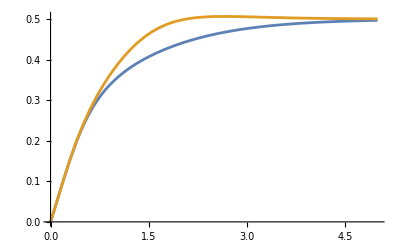

```mathematica
Plot[{CSz1, CSz1App}, {β, 0, 5}, PlotRange->Full]
```

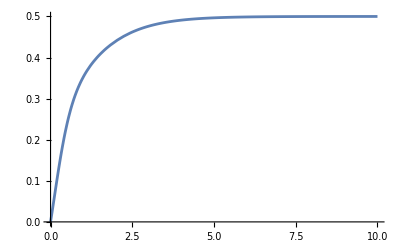

```mathematica
Plot[CSz1, {β, 0, 10}, PlotRange->Full]
```

```mathematica
OnePt = (1/48 (β^3 Sinh[2 hz β]+(6 hz (8+4 β+β^2) Sinh[2 √(hz^2) β])/(√(hz^2))))/(-β+1/2 ⅇ^(-2 √(hz^2) β) β+1/2 ⅇ^(2 √(hz^2) β) β+4 β^2-2 β^3+1/2 β^2 Cosh[hz β]^2+4 Cosh[√(hz^2) β]^2+1/12 β^3 Sinh[hz β]^2)/.hz->1/.β-> 1/T;
CSz1 = Tr[Sz1.MatrixExp[β Hxxz]]/Tr[MatrixExp[β Hxxz]]/.hz->1/.β-> 1/T;
```

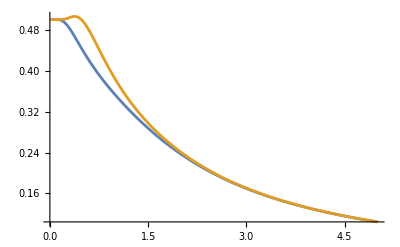

```mathematica
Plot[{CSz1, OnePt}, {T, 0.01, 5}, PlotRange->Full]
```

## Example: Sheet

### Lattice

```mathematica
L=1;
Λ = Flatten[Table[{i, j, 0}, {i, -L, L},{j,-L,  L}],1]
λ = Length[Λ];
```

{{-1,-1,0},{-1,0,0},{-1,1,0},{0,-1,0},{0,0,0},{0,1,0},{1,-1,0},{1,0,0},{1,1,0}}

```mathematica
ListPointPlot3D[Λ]
```

-Graphics3D-

### Interaction Tensors

#### XXZ

```mathematica
J=1;
V[v1_,v2_, s1_, s2_]:= If[Norm[v1-v2]==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) ||(s1==3&&s2==3), J, 0], 0];
```

```mathematica
V[{0,0,0}, {1, 0, 0}, 3, 3]
```

1

#### XX

```mathematica
J=1;
V[v1_,v2_, s1_, s2_]:= If[Norm[v1-v2]==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , J, 0], 0];
```

```mathematica
V[{1,0, 0}, {2, 0, 0}, 1, 2]V[{1, 0, 0}, {1, 0, 0}, 1 ,2]
```

0

```mathematica
Off[NIntegrate::izero]
```

### Correlation Function: XX

```mathematica
acc = 2;
vIndex= 5;
sIndex=3;
t=0;
```

```mathematica
ZT = Table[{T,Z[acc,1/T]}, {T, 10, 11, .2}]
```

{{10.,567.339},{10.2,565.13},{10.4,563.052},{10.6,561.095},{10.8,559.248},{11.,557.505}}

```mathematica
OzTun = Table[OnePoint[acc,1/T, vIndex, sIndex, t], {T, 10, 11, .2}];
```

```mathematica
OzTun
```

{27.7443,27.1167,26.518,25.9463,25.3998,24.8767}

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

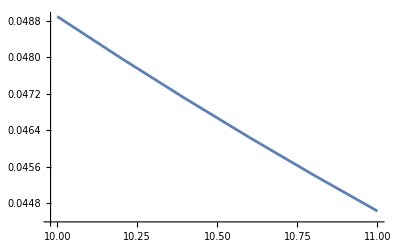

```mathematica
ListPlot[OzT, Joined->True]
```

### Correlation Function: XXZ

```mathematica
acc = 2;
vIndex= 5;
sIndex=3;
t=0;
```

```mathematica
ZT = Table[{T, Z[acc,1/T]}, {T, 10, 11, .2}];
```

```mathematica
ZT
```

{{10.,572.992},{10.2,570.524},{10.4,568.203},{10.6,566.019},{10.8,563.96},{11.,562.018}}

```mathematica
ZT = Table[{T, NZ[acc,1/T]}, {T, 0.1, 5, .2}];
```

```mathematica
OzTun = Table[OnePoint[acc,1/T, vIndex, sIndex, t], {T, 10, 11, .2}];
```

```mathematica
OzTun
```

{30.6735,29.9215,29.2063,28.5252,27.876,27.2562}

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

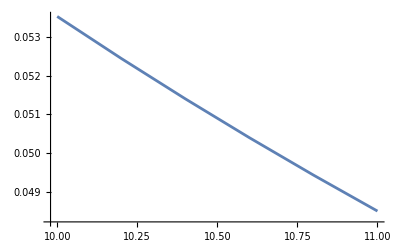

```mathematica
ListPlot[OzT, Joined->True]
```

## Example: Double Sheet

### Lattice

```mathematica
L=1;
Λ1 = Flatten[Table[{i, j, 0}, {i, -L, L},{j,-L,  L}],1];
Λ2= Flatten[Table[{i, j, 1}, {i, -L, L},{j,-L,  L}],1];
Λ = Union[Λ1,Λ2]
λ = Length[Λ];
```

{{-1,-1,0},{-1,-1,1},{-1,0,0},{-1,0,1},{-1,1,0},{-1,1,1},{0,-1,0},{0,-1,1},{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,-1,0},{1,-1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
FullGraphics[ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]]
```

FullGraphics[-Graphics3D-]

### Interaction Tensors

#### XXZ

```mathematica
J=1;
V[v1_,v2_, s1_, s2_]:= If[Norm[v1-v2]==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) ||(s1==3&&s2==3), J, 0], 0];
```

```mathematica
V[{0,0,0}, {1, 0, 0}, 3, 3]
```

1

#### XX

```mathematica
J=1;
V[v1_,v2_, s1_, s2_]:= If[Norm[v1-v2]==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , J, 0], 0];
```

```mathematica
V[{1,0, 0}, {2, 0, 0}, 1, 2]V[{1, 0, 0}, {1, 0, 0}, 1 ,2]
```

0

```mathematica
Off[NIntegrate::izero]
```

### Correlation Function: XX

```mathematica
acc = 1;
vIndex= 9;
sIndex=3;
t=0;
```

```mathematica
ZT = Table[{T, Z[acc,1/T]}, {T, 10, 11, .2}];
```

```mathematica
OzTun = Table[OnePoint[acc,1/T, vIndex, sIndex, t], {T, 10, 11, .2}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

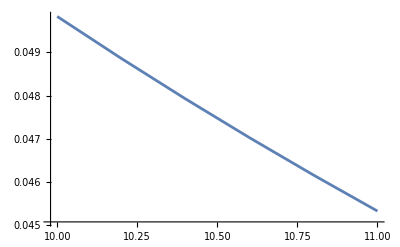

```mathematica
ListPlot[OzT, Joined->True]
```

### Correlation Function: XXZ

```mathematica
acc = 1;
vIndex= 9;
sIndex=3;
t=0;
```

```mathematica
ZT2 = Table[{T, Z[acc,1/T]}, {T, 10, 11, .2}];
```

```mathematica
OzTun2 = Table[OnePoint[acc,1/T, vIndex, sIndex, t], {T, 10, 11, .2}];
```

```mathematica
OzT2= Table[{ZT2[[k]][[1]],OzTun2[[k]]/ZT2[[k]][[2]]}, {k, 1, Length[ZT]}];
```

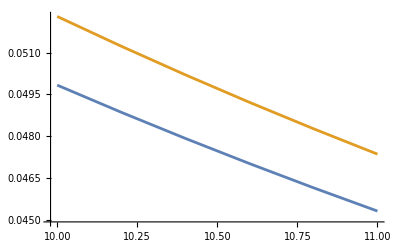

```mathematica
ListPlot[{OzT, OzT2}, Joined->True]
```

## Example: Double Sheet

### Lattice

```mathematica
L=1;
Λ1 = Flatten[Table[{i, j, 0}, {i, -L, L},{j,-L,  L}],1];
Λ2= Flatten[Table[{i, j, 1}, {i, -L, L},{j,-L,  L}],1];
Λ = Union[Λ1,Λ2]
λ = Length[Λ];
```

{{-1,-1,0},{-1,-1,1},{-1,0,0},{-1,0,1},{-1,1,0},{-1,1,1},{0,-1,0},{0,-1,1},{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,-1,0},{1,-1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
FullGraphics[ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]]
```

FullGraphics[-Graphics3D-]

### Interaction Tensors

#### Dipole Interaction

```mathematica
Simplify[({{1/2, -I/2, 0}, {1/2, I/2, 0}, {0, 0, 1}}).({{1/2, 1/2, 0}, {-I/2, I/2, 0}, {0, 0, 1}})]//MatrixForm
```

(0 | 1/2 | 0
1/2 | 0 | 0
0 | 0 | 1)

```mathematica
Simplify[-({{1/2, -I/2, 0}, {1/2, I/2, 0}, {0, 0, 1}}).({{3 dx^2- r^2, 3dy dx, 3 dz dx}, {3dx dy, 3 dy^2- r^2, 3dy dz}, {3dx dz, 3dy dz, 3 dz^2- r^2}}).({{1/2, 1/2, 0}, {-I/2, I/2, 0}, {0, 0, 1}})]//MatrixForm
```

(-3/4 (dx-ⅈ dy)^2 | 1/4 (-3 dx^2-3 dy^2+2 r^2) | -3/2 (dx-ⅈ dy) dz
1/4 (-3 dx^2-3 dy^2+2 r^2) | -3/4 (dx+ⅈ dy)^2 | -3/2 (dx+ⅈ dy) dz
-3/2 (dx-ⅈ dy) dz | -3/2 (dx+ⅈ dy) dz | -3 dz^2+r^2)

```mathematica
a=1;
b=1;
c=2.27;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
Ja=-29.20;
Jb=-29.20;
Jc=0.43;
Ds =0.54;
(*spin-spin exchange interaction*)
V1[v1_,v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
r = Norm[(v1-v2)];
If[r!=1,Return[0] ];
dx= Norm[(v1-v2)[[1]]];
If[dx==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Ja/2], If[s1==3&&s2==3, Return[Ja]]]];
dy= Norm[(v1-v2)[[2]]];
If[dy==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jb/2], If[s1==3&&s2==3, Return[Jb]]]];
dz= Norm[(v1-v2)[[3]]];
If[dz==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jc/2], If[s1==3&&s2==3, Return[Jc]]]];
Return[0];
]
(*dipoloe interaction*)
V2[v1_, v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
If[v1==v2, Return[0]];
r = Norm[LS.(v1-v2)];
dx= (LS. v1-v2)[[1]];
dy= (LS. v1-v2)[[2]];
dz= (LS. v1-v2)[[3]];
If[s1==1&&s2==1, Return[3/4 Ds (dx-ⅈ dy)^2/r^5]];
If[s1==1&&s2==2, Return[1/4 Ds(3 dx^2+3 dy^2-2 r^2)/r^5]];
If[s1==1&&s2==3, Return[3/2 Ds(dx-ⅈ dy) dz/r^5]];
If[s1==2&&s2==1, Return[1/4 Ds(3 dx^2+3 dy^2-2 r^2)/r^5]];
If[s1==2&&s2==2, Return[3/4 Ds(dx+ⅈ dy)^2/r^5]];
If[s1==2&&s2==3, Return[3/2 Ds (dx+ⅈ dy) dz/r^5]];
If[s1==3&&s2==1, Return[3/2 Ds(dx-ⅈ dy) dz/r^5]];
If[s1==3&&s2==2, Return[3/2 Ds(dx+ⅈ dy) dz/r^5]];
If[s1==3&&s2==3, Return[Ds(3 dz^2-r^2)/r^5]];
Return[0];
]
V[v1_, v2_, s1_, s2_]:= V1[v1, v2, s1, s2]+V2[v1, v2, s1, s2];
```

```mathematica
Table[V[{0,0,0}, {1, 4, 0}, i, j],{i, 1, 3}, {j, 1, 3} ]//MatrixForm//N
```

(-0.0000776261-0.0000414006 ⅈ | -0.000312229 | 0.
-0.000312229 | -0.0000776261+0.0000414006 ⅈ | 0.
0. | 0. | -0.000800411)

### Correlation Function: dipole, Sz

```mathematica
acc = 1;
vIndex= 9;
sIndex=3;(*Subscript[S, z] spin operator*)
t=0;
```

```mathematica
ZT = Table[{T, Z[acc,1/T]}, {T, 10, 11, .2}];
```

```mathematica
OzTun = Table[OnePoint[acc,1/T, vIndex, sIndex, t], {T, 10, 11, .2}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

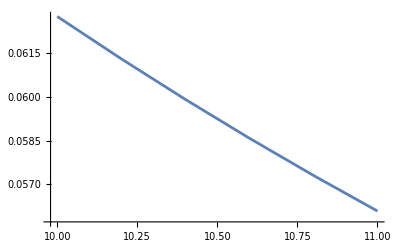

```mathematica
ListPlot[OzT, Joined->True]
```

### Correlation Function: dipole, Sx and Sy

```mathematica
(*S_+ = Subscript[S, x]+I Subscript[S, y]; S_- = Subscript[S, x] - I Subscript[S, y]*)
```

```mathematica
acc = 1;
vIndex= 9;
sIndex1=1;
sIndex2 =2;
t=0;
```

```mathematica
ZT = Table[{T, Z[acc,1/T]}, {T, 10, 11, .2}];
```

```mathematica
OpTun = Table[OnePoint[acc,1/T, vIndex, sIndex1, t], {T, 10, 11, .2}];
```

```mathematica
OmTun = Table[OnePoint[acc,1/T, vIndex, sIndex2, t], {T, 10, 11, .2}];
```

```mathematica
OxT= Table[{ZT[[k]][[1]],(OpTun[[k]] + OmTun[[k]] )/(2ZT[[k]][[2]])}, {k, 1, Length[ZT]}]//Chop
OyT= Table[{ZT[[k]][[1]],(-I)(OpTun[[k]] - OmTun[[k]] )/(2ZT[[k]][[2]])}, {k, 1, Length[ZT]}]//Chop
```

{{10.,0},{10.2,0},{10.4,0},{10.6,0},{10.8,0},{11.,0}}

{{10.,0},{10.2,0},{10.4,0},{10.6,0},{10.8,0},{11.,0}}

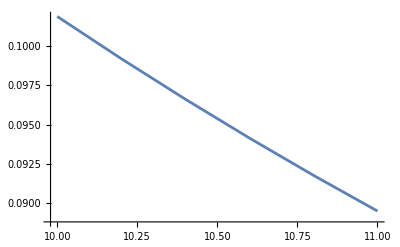

```mathematica
ListPlot[OzT, Joined->True]
```